```mathematica
(*Parameters*)
ClearAll["Global`*"]
μ=1;
a=1;
l=1;
λ = 20;
```

```mathematica
Clear[Adenom]
A[g_,l_,k_]:=k*g*a^2*(SphericalBesselJ[l,k*a])^2/(1-I*k*g*a^2*SphericalBesselJ[l,k*a]*SphericalHankelH1[l,k*a])
(*A[g_,l_,k_]=k*g*a^2*(SphericalBesselJ[l,k*a])^2/(1-I*k*g*a^2*(SphericalBesselJ[l,k*a])^2+k*g*a^2*SphericalBesselJ[l,k*a]*SphericalBesselY[l,k*a])*)
Adenom[g_,l_,k_]:=1-I*k*g*a^2*SphericalBesselJ[l,k*a]*SphericalHankelH1[l,k*a]
```

```mathematica
NSolve[Adenom[λ,l,k]==0 && Abs[k]<10,k]
ComplexPlot3D[A[λ,l,k],{k,-10-2I,10+2I}]
```

{{k→-8.06304-0.128157 ⅈ},{k→-4.7143-0.0506794 ⅈ},{k→0.-0.946729 ⅈ},{k→0.+9.89793 ⅈ},{k→4.7143-0.0506794 ⅈ},{k→8.06304-0.128157 ⅈ}}

-Graphics3D-

```mathematica
Clear[PsiU]
T[g_,L_,k_,p_,q_]=-((λ*a^2)/(4*Pi^2*μ))*(SphericalBesselJ[L,p*a]*SphericalBesselJ[L,q*a])/(1-I*k*g*a^2*SphericalBesselJ[L,k*a]*SphericalHankelH1[L,k*a]);
TD[g_,L_,k_]:=(1-I*k*g*a^2*SphericalBesselJ[L,k*a]*SphericalHankelH1[L,k*a]);
λprime[g_,L_,k_]=λ/(1+I*2*k*g*a^2*(SphericalBesselJ[L,k*a])^2);

Nnorm = 1;
kres=(4.714304496999773-0.05067937205151212 ⅈ);
Eres=kres^2/(2μ)
kresreal = Re[kres];
(* Note the -k in λ due to the PsiU function being an eigenvector of -kres*)
PsiU[g_,L_,k_,p_]=-4*Pi*λprime[g,L,-k]*a^2*Nnorm*SphericalBesselJ[L,p*a]*SphericalBesselJ[L,k*a]/(k^2-p^2);
PsiUNormalized[g_,L_,k_,p_]=-4*Pi*λprime[g,L,-k]*a^2*Nnorm*SphericalBesselJ[L,p*a]*SphericalBesselJ[L,k*a];
TFactorized[g_,L_,k_,p_,q_]=(1/(2μ))^2(kres^2-p^2)*(kres^2-q^2)*PsiU[λ,L,kres,p]*PsiU[λ,L,kres,q]/(kres^2-k^2);
TFactorized1[g_,L_,k_,p_,q_]=16*λprime[g,L,k]^2*Pi^2*a^4*SphericalBesselJ[L,p*a]*SphericalBesselJ[L,q*a]*(SphericalBesselJ[l,k*a])^2/(kres^2-k^2);

buffer = 0.3;
AbsArgPlot[T[λ,l,z,z,z],{z,kresreal-buffer,kresreal+buffer}]
AbsArgPlot[TFactorized[λ,l,z,z,z],{z,kresreal-buffer,kresreal+buffer}]
AbsArgPlot[1/(kres^2-z^2),{z,kresreal-buffer,kresreal+buffer}]
AbsArgPlot[PsiU[λ,l,kres,z],{z,0,2}]
AbsArgPlot[(1/(2μ))^2*(kres^2-z^2)*PsiU[λ,l,kres,z]*PsiU[λ,l,kres,z],{z,kresreal-buffer,kresreal+buffer}]
AbsArgPlot[TFactorized1[λ,l,z,z,z],{z,kresreal-buffer,kresreal+buffer}]
```

11.111-0.238918 ⅈ

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

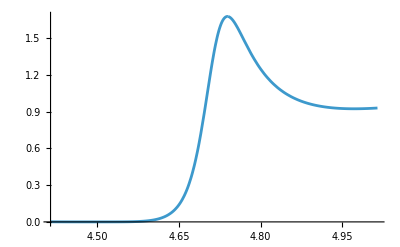

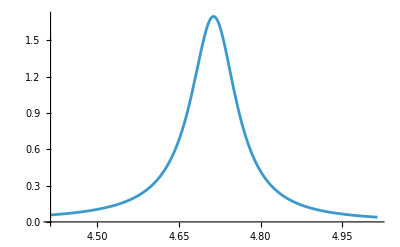

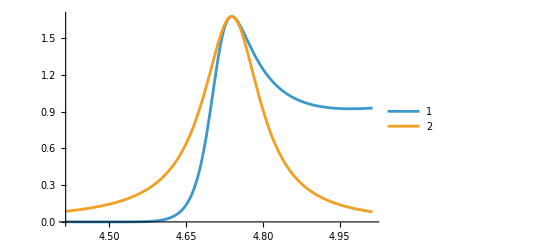

-4.02158-0.999991 ⅈ

1.3057+0.220296 ⅈ

XSExpansion[20,1,z]

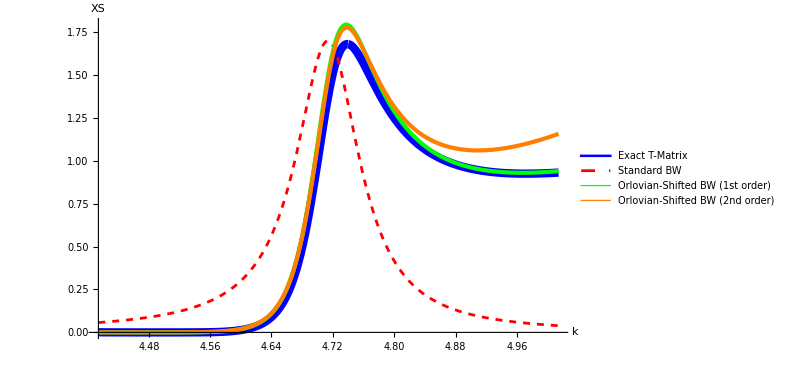

```mathematica
Clear[Gamma0,XS0]
XS[g_,L_,k_]=(64Pi^5μ^2)*(2L+1)Abs[T[g,L,k,k,k]]^2;
XSFactorized[g_,L_,k_]=(64Pi^5μ^2)*(2L+1)Abs[TFactorized[g,L,k,k,k]]^2;
BW[g_,L_,k_]=(4Pi/k^2)(2L+1)*Im[Eres]^2/((k^2/(2μ)-Re[Eres])^2+Im[Eres]^2);


Plot[XS[λ,l,z],{z,kresreal-buffer,kresreal+buffer}]
Plot[BW[λ,l,z],{z,kresreal-buffer,kresreal+buffer}]

k0=z/.FindRoot[Re[TD[λ,l,z]]==0,{z,-Re[kres]}];
Gamma0[g_,L_,kroot_]:=2*Im[TD[g,L,kroot]]/(Re[(μ/k*D[TD[g,L,k],k])/.k->kroot])
XS0[g_,L_,k_,kroot_]:=(4Pi/k^2)(2L+1)*(Gamma0[λ,L,kroot]^2/4)/((k^2/(2μ)-kroot^2/(2μ))^2+(Gamma0[λ,L,kroot]^2/4));

Plot[{XS[λ,l,z],XS0[λ,l,z,k0]},{z,kresreal-buffer,kresreal+buffer},PlotLegends->Automatic]
(*Plot[{XS[λ,l,z]},{z,0,10}]
Plot[XSFactorized[λ,l,z],{z,0,10}]*)

(**)
c1=-(D[PsiUNormalized[λ,l,kres,z],z]/.z->kres)/PsiUNormalized[λ,l,kres,kres]
c2=(-(D[PsiUNormalized[λ,l,kres,z],{z,2}]/.z->kres)/PsiUNormalized[λ,l,kres,kres])/2
XSExpansion1[g_,L_,k_]=BW[g,L,k]*Abs[1+(kres-k)*c1]^4;
XSExpansion2[g_,L_,k_]=BW[g,L,k]*Abs[1+(kres-k)*c1+(kres-k)^2*c2]^4;
(*XSExpansionExpansion[g_,L_,k_]=BW[g,L,k]*(1+4*Re[(kres-k)*c1]);*)
XSExpansion[λ,1,z]
Plot[{XS[λ,l,z],BW[λ,l,z],XSExpansion1[λ,l,z],XSExpansion2[λ,l,z]},{z,kresreal-buffer,kresreal+buffer},PlotStyle->{{Blue,Thickness[0.01]},(*Exact:Thick Blue*){Red,Dashed},(*Standard BW:Dashed Red*){Green,Thickness[0.005]}     (*Perturbative 1st order:Thin Green*),{Orange,Thickness[0.005]}     (*Perturbative 2nd order:Thin Orange*)},PlotLegends->{"Exact T-Matrix","Standard BW","Orlovian-Shifted BW (1st order)","Orlovian-Shifted BW (2nd order)"},AxesLabel->{"k","XS"},ImageSize->600]
```